Eigenvalue from power method: -3.99613

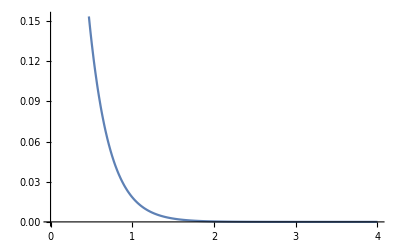

From the book we have that If λ is an eigenvalue of the matrix A and if v is an accompanying eigenvector, then one solution of the differential equation x = Ax is x(t) = e λt v. Thus we can make a plot with the smallest eigenvalue and eigenvector to get a distrobution of our solutions. Hence, we can say that asympotic behavior of the solutions approaches 0

```mathematica
X = SparseArray[{
Band[{1,1}] ->-2.,
Band[{1,2}] ->1.,
Band[{2,1}]->1.
}, {100,100}
];

u = Table[1,100];
For[i = 1, i < 8000, i++,
u = X.u/u[[1]];
]
Print["Eigenvalue from power method: ", u[[1]]]

Print[Plot[Exp[u[[1]]*x], {x,0,4}]]

Print["From the book we have that If λ is an eigenvalue of the matrix A and if v is an accompanying eigenvector, then one solution of the differential equation x = Ax is x(t) = e λt v. Thus we can make a plot with the smallest eigenvalue and eigenvector to get a distrobution of our solutions. Hence, we can say that asympotic behavior of the solutions approaches 0"]
```